#### Valores experimentales del silicio

```mathematica
hb=6.582119569*10^(-16);
```

```mathematica
datos0=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Programas\\ParteIm.csv"];
(*Se eliminan los encabezados de los datos*)
datos1=Drop[datos0,1];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Drop[datos1[[All,2]],{1,20}];
(*Se toma a la primera columna como el vector de energía*)
omega=Drop[datos1[[All,1]],{1,20}];
```

```mathematica
parteReKK1=kkrebook[omega,parteIm];
parteReSSKK1=sskkrebook[omega,parteIm,1.65,19.3548];
parteImKK1=kkimbook[omega,parteReKK1];
```

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Clear[selfconsbook]
```

```mathematica
prueba=selfconsbook[omega,parteReKK1,parteIm,1,0.3];
```

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Transpose[{omega,parteReKK1}]
```

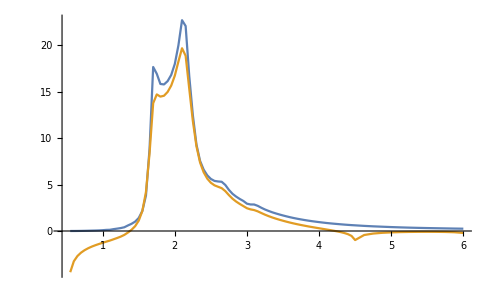

```mathematica
ListLinePlot[{Transpose[{omega,parteIm}],Transpose[{omega,prueba[[2]]}]},PlotRange->All]
```

## Modelo de Drude

```mathematica
omegaMin=2; (*valor mínimo de energía*)
omegaMax=8; (*valor máximo de energía*)
omega10=Range[0.1,10,0.01];(*rango de energías*)
omegaPAl=5.142; (*frecuencia de plasma Al*)
gammaAl=0.147; (*constante de amortuguamiento Al*)
```

```mathematica
(*Se define el modelo de drude*)
epsDrude[ω_,ωp_,γ_]:=1-((ωp)^2/(ω*(ω+ I γ)))
epsLorentz[A_,ω_,ω0_,γ_]:=1+A^2/(ω0^2-ω^2-I*(γ ω))
(*Se define la parte real y la imaginaria del índice de refracción*)
epsImagDrude[energy_,omegaP_,gamma_]:=Im[epsDrude[energy,omegaP,gamma]];
epsReDrude[energy_,omegaP_,gamma_]:=Re[epsDrude[energy,omegaP,gamma]];

epsImagLorentz[A_,ω_,ω0_,γ_]:=Im[epsLorentz[A,ω,ω0,γ]];
epsReLorentz[A_,ω_,ω0_,γ_]:=Re[epsLorentz[A,ω,ω0,γ]];
```

```mathematica
realLorentz=Table[{omega,epsReLorentz[2,omega,omegaPAl,gammaAl]},{omega,0.1,10,0.01}];
imagLorentz=Table[{omega,epsImagLorentz[2,omega,omegaPAl,gammaAl]},{omega,0.1,10,0.01}];
```

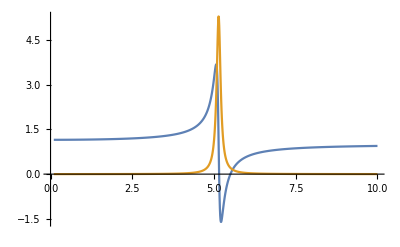

```mathematica
ListLinePlot[{realLorentz,imagLorentz},PlotRange->All]
```

```mathematica
omegas1=Range[0.1,4,0.01];
realLorentz1=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas1}];
imagLorentz1=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas1}];
parteReKK1Lorentz=kkrebook[omegas1,imagLorentz1[[All,2]]];
parteImKK1Lorentz=kkimbook[omegas1,realLorentz1[[All,2]]];
omegas2=Range[0.1,5,0.01];
realLorentz2=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas2}];
imagLorentz2=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas2}];
parteReKK2Lorentz=kkrebook[omegas2,imagLorentz2[[All,2]]];
parteImKK2Lorentz=kkimbook[omegas2,realLorentz2[[All,2]]];
omegas3=Range[0.1,7,0.01];
realLorentz3=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas3}];
imagLorentz3=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas3}];
parteReKK3Lorentz=kkrebook[omegas3,imagLorentz3[[All,2]]];
parteImKK3Lorentz=kkimbook[omegas3,realLorentz3[[All,2]]];
omegas4=Range[0.1,10,0.01];
realLorentz4=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas4}];
imagLorentz4=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas4}];
parteReKK4Lorentz=kkrebook[omegas4,imagLorentz4[[All,2]]];
parteImKK4Lorentz=kkimbook[omegas4,realLorentz4[[All,2]]];
omegas5=Range[0.1,15,0.01];
realLorentz5=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas5}];
imagLorentz5=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas5}];
parteReKK5Lorentz=kkrebook[omegas5,imagLorentz5[[All,2]]];
parteImKK5Lorentz=kkimbook[omegas5,realLorentz5[[All,2]]];
```

```mathematica
listImag={imagLorentz5,Transpose[{omegas1,parteImKK1Lorentz}],Transpose[{omegas2,parteImKK2Lorentz}],Transpose[{omegas3,parteImKK3Lorentz}],Transpose[{omegas4,parteImKK4Lorentz}],Transpose[{omegas5,parteImKK5Lorentz}]};
listRe={realLorentz5,Transpose[{omegas1,parteReKK1Lorentz}],Transpose[{omegas2,parteReKK2Lorentz}],Transpose[{omegas3,parteReKK3Lorentz}],Transpose[{omegas4,parteReKK4Lorentz}],Transpose[{omegas5,parteReKK5Lorentz}]};
```

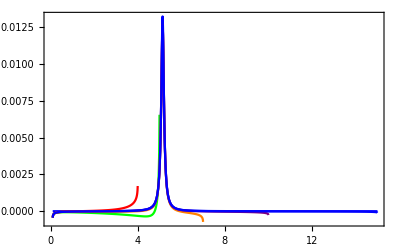
-Graphics--Graphics--Graphics-

```mathematica
Labeled[ListLinePlot[listImag,PlotRange->All,PlotStyle->{Blue,Red,Green,Orange,Purple},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

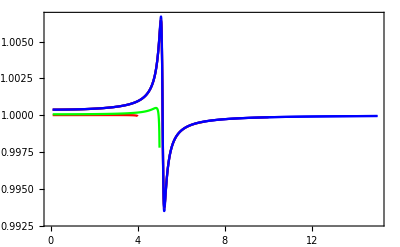
-Graphics--Graphics--Graphics-

```mathematica
Labeled[ListLinePlot[listRe,PlotRange->All,PlotStyle->{Blue,Red,Green,Orange,Purple},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon'(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

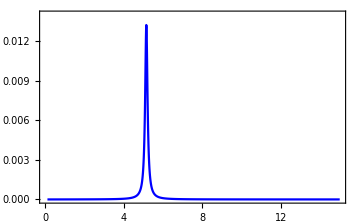
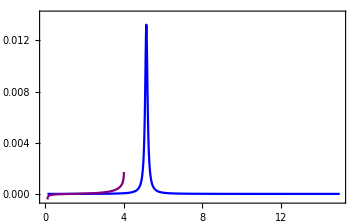
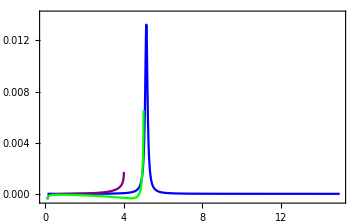
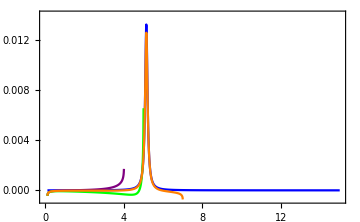
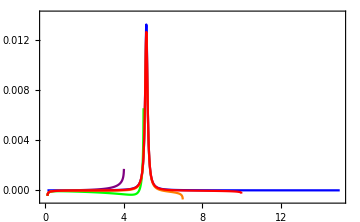
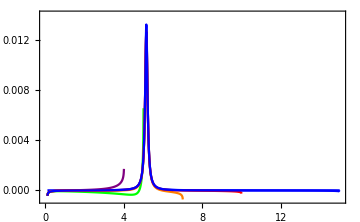
{-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
algo = Labeled[ListLinePlot[listImag[[1;;#]],PlotRange->{{0,15},{Automatic,0.014}},ImageSize->Medium,PlotStyle->{Blue,Purple,Green,Orange,Red},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]&/@Range[1,Length[listImag]]
```

```mathematica
Export["lorentzKKIm.svg",algo]
```

lorentzKKIm.svg

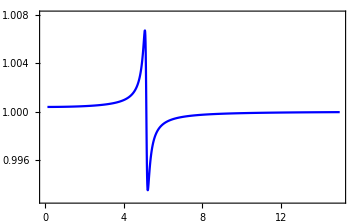
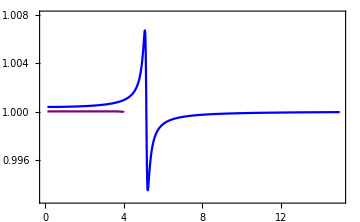
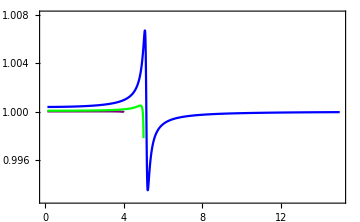
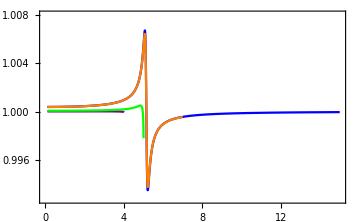
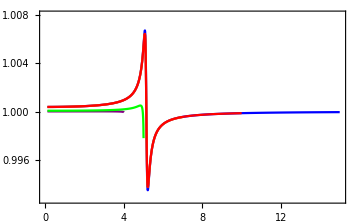
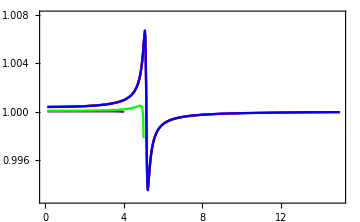
{-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
algo2= Labeled[ListLinePlot[listRe[[1;;#]],PlotRange->{{0,15},{Automatic,1.008}},ImageSize->Medium,PlotStyle->{Blue,Purple,Green,Orange,Red},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon'(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]&/@Range[1,Length[listRe]]
```

```mathematica
Export["lorentzKKRe.svg",algo2]
```

lorentzKKRe.svg

```mathematica
Export["listRe.gif",algo2,"DisplayDurations"->1/2]
Export["listImag.gif",algo,"DisplayDurations"->1/2]
```

listRe.gif

listImag.gif

```mathematica
SetDirectory["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Figuras"]
```

C:\Users\Nanoplasmonics\Documents\GitHub\Tesis-de-Licenciatura\Figuras

```mathematica
listImagKK={Transpose[{datosLambda,kk28im}],Transpose[{omega10,parteImKK28}]};
listReKK={Transpose[{datosLambda,kk28re}],Transpose[{omega10,parteReKK28}]};
```

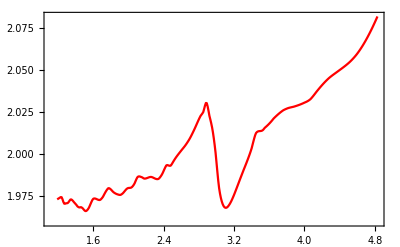
-Graphics--Graphics--Graphics-

```mathematica
eps28ReExp=Labeled[ListLinePlot[Table[{x,eps28Re[x]},{x,1.19,4.83,0.01}],PlotRange->All,PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon'(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

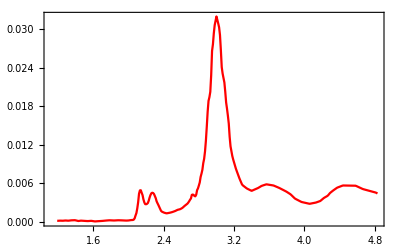
-Graphics--Graphics--Graphics-

```mathematica
eps28ImExp=Labeled[ListLinePlot[Table[{x,eps28Im[x]},{x,1.19,4.83,0.01}],PlotRange->All,PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\\omega)"],Magnification->1.5],Style[MaTeX["\\hbar\\omega\: [\\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

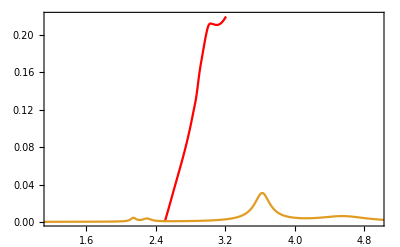
-Graphics--Graphics--Graphics-

```mathematica
eps28ImKK=Labeled[ListLinePlot[listImagKK,PlotRange->{{1.19,4.95},{0,0.22}},PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

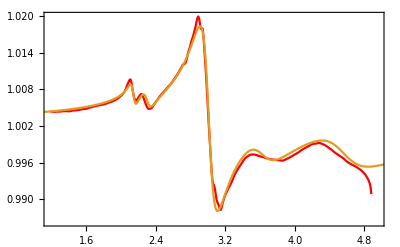
-Graphics--Graphics--Graphics-

```mathematica
eps28ReKK=Labeled[ListLinePlot[listReKK,PlotRange->{{1.19,4.95},{Automatic,Automatic}},PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

```mathematica
Export["eps28ReExp.svg",eps28ReExp]
Export["eps28ImExp.svg",eps28ImExp]
Export["eps28ReKK.svg",eps28ReKK]
Export["eps28ImKK.svg",eps28ImKK]
```

eps28ReExp.svg

eps28ImExp.svg

eps28ReKK.svg

eps28ImKK.svg

```mathematica
sale=sskkrebook[omega1, alImagDrude[[All,2]],omegaconocida, real1];
```

Set::setraw: Cannot assign to raw object {0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»}.

Set::setraw: Cannot assign to raw object 250.175.

Set::setraw: Cannot assign to raw object 239.227.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
(*Suponiendo que tengo la parte imaginaria*)
```

```mathematica
parteReKK1Drude=kkrebook[omega1,alImagDrude[[All,2]]];
parteImKK1Drude=kkimbook[omega1,parteReKK1Drude];
parteReKK12Drude=kkrebook[omega1,parteImKK1Drude];

(*Suponiendo que tengo la parte real*)
parteImKK2Drude=kkimbook[omega1,alRealDrude[[All,2]]];
parteReKK2Drude=kkrebook[omega1,parteImKK2Drude];
```

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object 0.483227.

Set::setraw: Cannot assign to raw object 0.482506.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

$Aborted

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object {2.05589,1.9006,1.82246,1.77008,1.73059,1.69885,1.67228,1.64942,1.62934,1.61142,«5991»}.

$Aborted

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object {-1.03341,-0.647078,-0.490543,-0.397043,-0.33202,-0.282953,-0.243985,-0.211938,-0.184901,-0.161646,«5991»}.

$Aborted

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object -5.57452.

Set::setraw: Cannot assign to raw object -5.56799.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

$Aborted

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object {14.3658,12.2593,11.2012,10.493,9.95985,9.5319,9.17414,8.86656,8.59667,8.35611,«5991»}.

$Aborted

```mathematica
selfDrude1=selfconsbook[omega1,alRealDrude[[All,2]],parteImKK2Drude,10,0.5];
selfDrude2=selfconsbook[omega1,alImagDrude[[All,2]],parteReKK1Drude,10,0.5];
```

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object -5.57452.

Set::setraw: Cannot assign to raw object -5.56799.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pkspec1: The expression j$6808197 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

$Aborted

Set::setraw: Cannot assign to raw object {2.,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,«5991»}.

Set::setraw: Cannot assign to raw object 0.483227.

Set::setraw: Cannot assign to raw object 0.482506.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pkspec1: The expression j$6993049 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

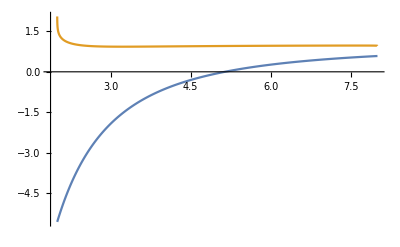

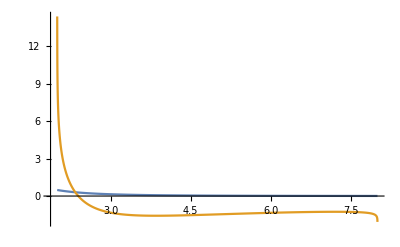

```mathematica
ListLinePlot[{alRealDrude,Transpose[{omega1,parteReKK1Drude}]},PlotRange->All]
ListLinePlot[{alImagDrude,Transpose[{omega1,parteImKK2Drude}]},PlotRange->All]
```

#### Valores experimentales de eritrocitos

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
datos0Im=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}],.];
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}],Method->"Spline"];
(*Se toma a la primera columna como el vector de energía*)
```

```mathematica
nExpLambda[x_]:=parteRe[h c/x]+I*parteIm[h c/x]
```

```mathematica
parteImLambda[x_]:=parteIm[h c/x]
parteReLambda[x_]:=parteRe[h c/x]
epsExp[x_]:=Sqrt[parteRe[x]+I*parteIm[x]]
```

```mathematica
parteImEq=Table[Im[epsExp[x]],{x,1.19,4.82,0.005}];
parteReEq=Table[Re[epsExp[x]],{x,1.19,4.82,0.005}];
omega=Range[1.19,4.82,0.005];
```

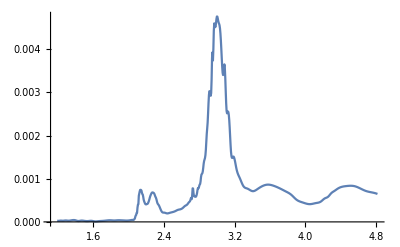

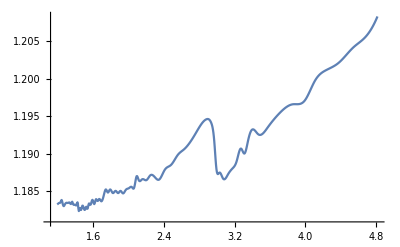

```mathematica
ListLinePlot[Transpose[{omega,parteImEq}],PlotRange->All]
ListLinePlot[Transpose[{omega,parteReEq}],PlotRange->All]
```

```mathematica
parteImKK0=kkimbook[omega,parteReEq];
parteReKK0=kkrebook[omega,parteImKK0];
parteImKK01=kkimbook[omega,parteReKK0];
parteReKK01=kkrebook[omega,parteImKK01];
parteImKK02=kkimbook[omega,parteReKK01];
```

Set::setraw: Cannot assign to raw object {1.19,1.195,1.2,1.205,1.21,1.215,1.22,1.225,1.23,1.235,«717»}.

Set::setraw: Cannot assign to raw object 1.18322.

Set::setraw: Cannot assign to raw object 1.18327.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.195,1.2,1.205,1.21,1.215,1.22,1.225,1.23,1.235,«717»}.

Set::setraw: Cannot assign to raw object {-0.366484,-0.308199,-0.279055,-0.259615,-0.245022,-0.233344,-0.223627,-0.215317,-0.208026,-0.201457,«717»}.

Part::pkspec1: The expression j$7266749 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.195,1.2,1.205,1.21,1.215,1.22,1.225,1.23,1.235,«717»}.

Set::setraw: Cannot assign to raw object 0.67669.

Set::setraw: Cannot assign to raw object 0.811868.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.195,1.2,1.205,1.21,1.215,1.22,1.225,1.23,1.235,«717»}.

Set::setraw: Cannot assign to raw object {0.0529162,-0.0795911,-0.107657,-0.118055,-0.122532,-0.124396,-0.124928,-0.124709,-0.124022,-0.123014,«717»}.

Part::pkspec1: The expression j$7270623 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.195,1.2,1.205,1.21,1.215,1.22,1.225,1.23,1.235,«717»}.

Set::setraw: Cannot assign to raw object 0.846062.

Set::setraw: Cannot assign to raw object 0.81905.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
parteReKK1=kkrebook[omega,parteImEq];
parteImKK1=kkimbook[omega,parteReKK1];
parteReKK11=kkrebook[omega,parteImKK1];
```

```mathematica
selfRe=selfconsbook[omega,parteReEq,parteImKK0,10,0.5];
selfIm=selfconsbook[omega,parteReKK1,parteImEq,10,0.5];
```

```mathematica
h c/400
```

3.10175

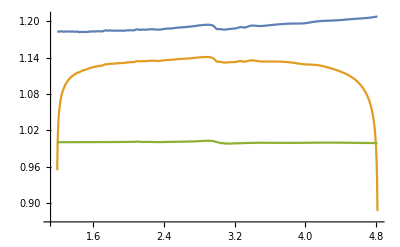

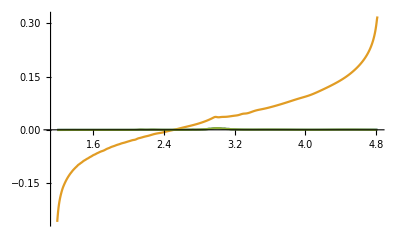

```mathematica
ListLinePlot[{Transpose[{omega,parteReEq}],Transpose[{omega,selfRe[[1]]}],Transpose[{omega,selfIm[[1]]}]},PlotRange->All]
ListLinePlot[{Transpose[{omega,parteImEq}],Transpose[{omega,selfRe[[2]]}],Transpose[{omega,selfIm[[2]]}]},PlotRange->All]
```

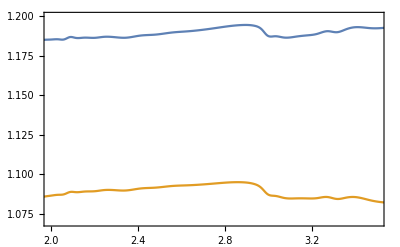

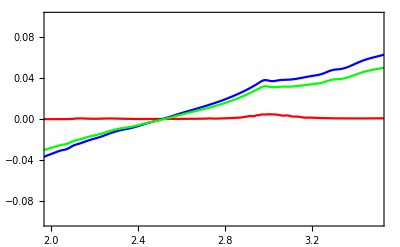

```mathematica
expplot=ListLinePlot[{Transpose[{omega,parteReEq}],Transpose[{omega,parteReKK0}]},PlotRange->{{2,3.5},{1.07,1.2}},PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotLegends->Placed[SwatchLegend[{Style["Datos experimentales",FontFamily->"Latin Modern Roman 10"],Style["KK1",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.5,0.7}];Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\varepsilon'(\omega)"],Magnification->1.6],None},{Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.6],None}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{90,10},{60,60}}]

expplot=ListLinePlot[{Style[Transpose[{omega,parteImEq}],Red],Style[Transpose[{omega,parteImKK0}],Blue],Style[Transpose[{omega,parteImKK01}],Green]},PlotRange->{{2,3.5},{-0.1,0.1}},PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotLegends->Placed[SwatchLegend[{Style["Datos experimentales",FontFamily->"Latin Modern Roman 10"],Style["KK1",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.5,0.7}];Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\varepsilon''(\omega)"],Magnification->1.6],None},{Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.6],None}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{90,10},{60,60}}]
```

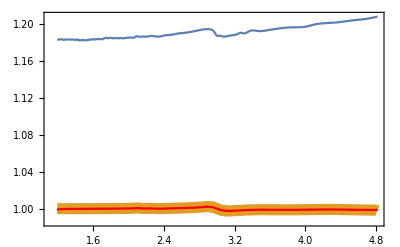

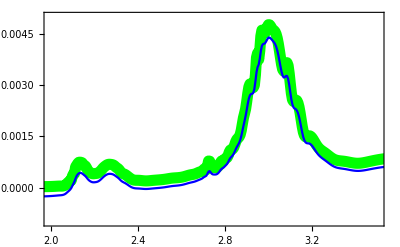

```mathematica
expplot=ListLinePlot[{Transpose[{omega,parteReEq}],Style[Transpose[{omega,parteReKK1}],Thickness[0.02]],Style[Transpose[{omega,parteReKK11}],Red]},PlotRange->All,PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotLegends->Placed[SwatchLegend[{Style["Datos experimentales",FontFamily->"Latin Modern Roman 10"],Style["KK1",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.5,0.7}];Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\varepsilon'(\omega)"],Magnification->1.6],None},{Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.6],None}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{90,10},{60,60}}]

expplot=ListLinePlot[{Style[Transpose[{omega,parteImEq}],Green,Thickness[0.02]],Style[Transpose[{omega,parteImKK1}],Blue]},PlotRange->{{2,3.5},{-0.001,0.005}},PlotStyle->{FontFamily->"Latin Modern Roman 10"},PlotLegends->Placed[SwatchLegend[{Style["Datos experimentales",FontFamily->"Latin Modern Roman 10"],Style["KK1",FontFamily->"Latin Modern Roman 10"]},LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.5,0.7}];Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],FrameLabel->{{Style[MaTeX["\varepsilon''(\omega)"],Magnification->1.6],None},{Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.6],None}},LabelStyle->{FontFamily->"Latin Modern Roman 10"},FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{90,10},{60,60}}]
```

```mathematica
ListLinePlot[{Transpose[{omega,parteReEq}],Transpose[{omega,parteReKK0}]},PlotRange->{{2.5,3.5},{1.15,1.5}}]
```

```mathematica
h c/400
h c/600
```

3.10175

2.06783

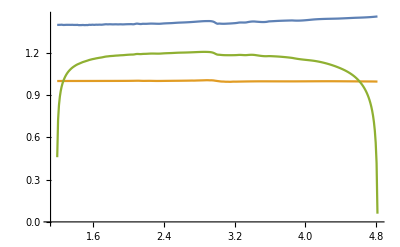

```mathematica
ListLinePlot[{Transpose[{omega,parteReEq}],Transpose[{omega,prueba[[1]]}],Transpose[{omega,parteReKK0}]},PlotRange->All]
```

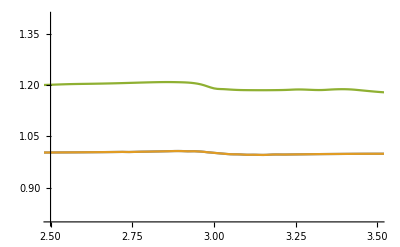

```mathematica
ListLinePlot[{Transpose[{omega,parteReKK1}],Transpose[{omega,prueba[[1]]}],Transpose[{omega,parteReKK0}]},PlotRange->{{2.5,3.5},{0.8,1.4}}]
```

```mathematica
h c/600
```

2.06783

```mathematica
parteRe[4]
```

1.43294

```mathematica
real1=parteRe[4];
omegaconocida=4;
sale=sskkrebook[omega, parteImEq,omegaconocida, real1];
```

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

Set::setraw: Cannot assign to raw object 0.0000817065.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

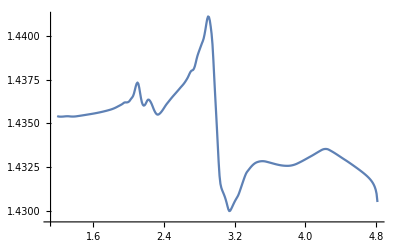

```mathematica
ListLinePlot[Transpose[{omega,sale}]]
```

#### Valores experimentales del oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kau=kau1[[All,2]];
```

```mathematica
ωAu
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

```mathematica
nInterpFunction=Interpolation[Transpose[{ωAu,nau}]];
kInterpFunction=Interpolation[Transpose[{ωAu,kau}]];
```

```mathematica
nAu=Table[nInterpFunction[x],{x,0.65,6.6,0.01}];
kAu=Table[kInterpFunction[x],{x,0.65,6.6,0.01}];
energy=Range[0.65,6.6,0.01];
```

```mathematica
nInterpFunction[3]
```

1.45997

```mathematica
parteReKKAu=kkrebook[energy,kAu];
parteImKKAu=kkimbook[energy,parteReKKAu];
pruebaAu10=selfconsbook[energy,parteReKKAu,kAu,20,0.5];
pruebaSelf=sskkrebook[energy,kAu,3,nInterpFunction[3]];
```

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

2

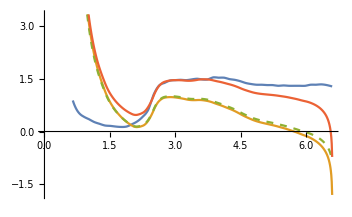

```mathematica
ListLinePlot[{Transpose[{energy,nAu}],Transpose[{energy,parteReKKAu}],Style[Transpose[{energy,pruebaAu10[[1]]}],Dashed],Transpose[{energy,pruebaSelf}]}]
```